## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
(* SAVE TO H5 FOR PySR*)
(*PbbsqA2Bvalueserrbars[ampname_,P1_,etavalue_]:=(
PbbsqA2BvalueerrbarLIST={};
PbaveragedbsquareA2B=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
forMakeErrBars = {};
Do[
AppendTo[forMakeErrBars,{{PbaveragedbsquareA2B[[i]][[1]],PbaveragedbsquareA2B[[i]][[2]]},PbaveragedbsquareA2B[[i]][[3]]}],{i, Length[PbaveragedbsquareA2B]}];
PbbsqA2Bvalueerrbar = MakeErrBars[forMakeErrBars];
Do[
AppendTo[PbbsqA2BvalueerrbarLIST, {etavalue, PbbsqA2Bvalueerrbar[[i]][[1]][[1]][[1]] ,PbbsqA2Bvalueerrbar[[i]][[1]][[1]][[2]],  PbbsqA2Bvalueerrbar[[i]][[1]][[2]],  PbbsqA2Bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[PbbsqA2Bvalueerrbar]}];
Return[PbbsqA2BvalueerrbarLIST]
)
ExporttoH5Amp[ampname_,P1_]:=(
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_Amp_Re_Im_err.h5",Table["Pl"<>ToString[P1]<>"/eta_"<>ToString[n]<>"_bL_bT_Im"<>ToString[ampname]<>"_err"->PbbsqA2Bvalueserrbars[ampname, P1, n],{n,1,10}],OverwriteTarget->"Append"];
)
Do[ExporttoH5Amp[A2B,-i],{i, 1,4}]*)
```

```mathematica
Import["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_Amp_Re_Im_err.h5","StructureGraph"]
```

-Graphics-

```mathematica
PlotAbLfordiffbLbT[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bL]];
PlotbLforDiffbTList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->bnum}],{bL,data}];
AppendTo[PlotbLforDiffbTList,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{, Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bL_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbL,"PDF",ImageResolution->600];
PlotbTforDiffbLList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bL->bLi, bNum->bnum}],{bT,data}];
AppendTo[PlotbTforDiffbLList,bLAmp];
 ,{bLi,bLlist}];
PlotbT= ErrorListPlot[Table[MakeErrBars[PlotbTforDiffbLList[[bLi]]],{bLi, Length[bLlist]}],FrameLabel->{,ampname b bnum}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bLlist[[bLi]]],{bLi,Length[bLlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bT_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbT,"PDF",ImageResolution->600];GraphicsRow[{PlotbL,PlotbT},ImageSize->Full]
)
PlotAfordiffBPbbsq[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
bsquarelist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bsquare]];
(*bsquarelist = Select[fullbsquarelist,8<=#<=25&];*)
Pb32by2Pilist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],Pb32by2Pi]];
PlotPbforDiffbsq={};
Do[
PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi, bNum->bnum}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsq,PbAmp];
 ,{bsqi,bsquarelist}];
PlotbP= ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsq[[bsqi]]],{bsqi, Length[bsquarelist]}],FrameLabel->{ , Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bsquarelist[[bsqi]]],{bsqi,Length[bsquarelist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bP_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->bnum}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bsq_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotbsq,"PDF",ImageResolution->600];
GraphicsRow[{PlotbP,Plotbsq},ImageSize->Full]
)
```

```mathematica
PlotAbLfordiffbLbT[A2B,-1,8, even, "Re"]
```

Re A2B =>  = -1 ,eta = 8

-Graphics-

```mathematica
PlotAfordiffBPbbsq[A2B,-1,8, even, "Re"]
```

Re A2B =>  = -1 ,eta = 8

-Graphics-

```mathematica
PlotAfordiffBPbbsq[ampname_,P1_,etavalue_,bnum_,Nnum_]:=Module[{fullbsquarelist,bsqListLT9,bsqListGE9,PlotPbforDiffbsqLT9,PlotPbforDiffbsqGE9,PbAmp,PlotbPLT9,PlotbPGE9},Print[Nnum," ",ampname," => \!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSubscriptBox[\nStyleBox[\"P\", \"TI\"], \nStyleBox[\"L\", \"TI\"]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"P_{L}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\) = ",P1," ,eta = ",etavalue];
(*1. Extract and partition bsquare list*)fullbsquarelist=Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],bsquare]];
bsqListLT9=Select[fullbsquarelist,#<9&];(*For|b| <3*)bsqListGE9=Select[fullbsquarelist,#>=9&];(*For|b| >=3*)(* ==========================================*)(* ============ |b| <3a PLOT===============*)(* ==========================================*)PlotPbforDiffbsqLT9={};
Do[PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi,bNum->bnum}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsqLT9,PbAmp];,{bsqi,bsqListLT9}];
PlotbPLT9=ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsqLT9[[i]]],{i,Length[bsqListLT9]}],FrameLabel->{"\!\(TraditionalForm\`\*StyleBox[\"P\", \"TI\"]·\*StyleBox[\"b\", \"TI\"] \*FractionBox[\(32\), \(2 π\)]\)",Nnum ampname},Frame->True,GridLines->Automatic,(*Added Grid*)PlotRange->Full,PlotLegends->Table["\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSuperscriptBox[\nRowBox[{\"(\", \nStyleBox[\"b\", \"TI\"], \")\"}], \"2\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"(b)^{2}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\) = "<>ToString[bsqListLT9[[i]]],{i,Length[bsqListLT9]}],ImageSize->450,PlotLabel->"|b| < 3a Data"];
Export["/Users/hariprashadravikumar/Downloads/bP_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>"_bLT3.pdf",PlotbPLT9,"PDF",ImageResolution->600];
(* ==========================================*)(* =========== |b| >=3a PLOT===============*)(* ==========================================*)PlotPbforDiffbsqGE9={};
Do[PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi,bNum->bnum}],{Pb32by2Pi,data}];
AppendTo[PlotPbforDiffbsqGE9,PbAmp];,{bsqi,bsqListGE9}];
PlotbPGE9=ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsqGE9[[i]]],{i,Length[bsqListGE9]}],FrameLabel->{"\!\(TraditionalForm\`\*StyleBox[\"P\", \"TI\"]·\*StyleBox[\"b\", \"TI\"] \*FractionBox[\(32\), \(2 π\)]\)",Nnum ampname},Frame->True,GridLines->Automatic,(*Added Grid*)PlotRange->Full,PlotLegends->Table["\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\nSuperscriptBox[\nRowBox[{\"(\", \nStyleBox[\"b\", \"TI\"], \")\"}], \"2\"], TraditionalForm], \"errors\" -> {}, \"input\" -> \"(b)^{2}\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\) = "<>ToString[bsqListGE9[[i]]],{i,Length[bsqListGE9]}],ImageSize->450,PlotLabel->"|b| >= 3a Data"];
Export["/Users/hariprashadravikumar/Downloads/bP_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>"_bGE3.pdf",PlotbPGE9,"PDF",ImageResolution->600];
(*Output both P.b plots side-by-side in the notebook*)GraphicsRow[{PlotbPLT9,PlotbPGE9},ImageSize->Full]]

PlotAfordiffBPbbsq[A12B,-1,8, even, "Re"]
```

Re A12B =>  = -1 ,eta = 8

-Graphics-

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
WeightList = {};
Do[
ε=10^-6;
σ=(MakeErrBars[{{1,xyJKf[[ii]][[3]]}}][[1]][[2]][[1]][[2]]);
AppendTo[WeightList,1/Max[σ,ε]^2], {ii, Length[xyJKf]}];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];
```

```mathematica
test =MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-1,etav->8, bNum->even}],{bL, bT,data}]
```

{{0,1,⟨-0.065(14)⟩_(RowBox[{)},{0,2,⟨-0.0185(26)⟩_(RowBox[{)},{0,3,⟨-0.0055(13)⟩_(RowBox[{)},{0,4,⟨-0.00139(80)⟩_(RowBox[{)},{0,5,⟨-0.00101(58)⟩_(RowBox[{)},{0,6,⟨-0.00144(48)⟩_(RowBox[{)},{0,7,⟨-540(370) × 10⟩_(RowBox[{)},{0,-1,⟨-0.055(14)⟩_(RowBox[{)},{0,-2,⟨-0.0196(27)⟩_(RowBox[{)},{0,-3,⟨-0.0070(13)⟩_(RowBox[{)},{0,-4,⟨-0.00350(83)⟩_(RowBox[{)},{0,-5,⟨-0.00217(61)⟩_(RowBox[{)},{0,-6,⟨-0.00156(47)⟩_(RowBox[{)},{0,-7,⟨-690(380) × 10⟩_(RowBox[{)},{1,1,⟨-0.0450(84)⟩_(RowBox[{)},{2,2,⟨-0.0088(15)⟩_(RowBox[{)},{3,3,⟨-0.00250(76)⟩_(RowBox[{)},{4,4,⟨-0.00132(49)⟩_(RowBox[{)},{5,5,⟨-440(340) × 10⟩_(RowBox[{)},{1,2,⟨-0.0150(20)⟩_(RowBox[{)},{2,4,⟨-0.00203(58)⟩_(RowBox[{)},{3,6,⟨-430(310) × 10⟩_(RowBox[{)},{2,1,⟨-0.0208(39)⟩_(RowBox[{)},{4,2,⟨-0.0018(12)⟩_(RowBox[{)},{6,3,⟨-110(640) × 10⟩_(RowBox[{)},{4,1,⟨-0.0025(24)⟩_(RowBox[{)},{8,2,⟨0.00005 ± 0.00086⟩_(RowBox[{)},{1,-1,⟨-0.0359(85)⟩_(RowBox[{)},{2,-2,⟨-0.0092(15)⟩_(RowBox[{)},{3,-3,⟨-0.00191(78)⟩_(RowBox[{)},{4,-4,⟨-820(510) × 10⟩_(RowBox[{)},{5,-5,⟨230(340) × 10⟩_(RowBox[{)},{1,-2,⟨-0.0151(21)⟩_(RowBox[{)},{2,-4,⟨-0.00275(58)⟩_(RowBox[{)},{3,-6,⟨-200(290) × 10⟩_(RowBox[{)},{2,-1,⟨-0.0170(40)⟩_(RowBox[{)},{4,-2,⟨-0.0038(12)⟩_(RowBox[{)},{6,-3,⟨200(630) × 10⟩_(RowBox[{)},{4,-1,⟨-0.0049(25)⟩_(RowBox[{)},{8,-2,⟨-730(850) × 10⟩_(RowBox[{)},{-1,1,⟨-0.0450(84)⟩_(RowBox[{)},{-2,2,⟨-0.0088(15)⟩_(RowBox[{)},{-3,3,⟨-0.00250(76)⟩_(RowBox[{)},{-4,4,⟨-0.00132(49)⟩_(RowBox[{)},{-5,5,⟨-440(340) × 10⟩_(RowBox[{)},{-1,2,⟨-0.0150(20)⟩_(RowBox[{)},{-2,4,⟨-0.00203(58)⟩_(RowBox[{)},{-3,6,⟨-430(310) × 10⟩_(RowBox[{)},{-2,1,⟨-0.0208(39)⟩_(RowBox[{)},{-4,2,⟨-0.0018(12)⟩_(RowBox[{)},{-6,3,⟨-110(640) × 10⟩_(RowBox[{)},{-4,1,⟨-0.0025(24)⟩_(RowBox[{)},{-8,2,⟨0.00005 ± 0.00086⟩_(RowBox[{)},{-1,-1,⟨-0.0359(85)⟩_(RowBox[{)},{-2,-2,⟨-0.0092(15)⟩_(RowBox[{)},{-3,-3,⟨-0.00191(78)⟩_(RowBox[{)},{-4,-4,⟨-820(510) × 10⟩_(RowBox[{)},{-5,-5,⟨230(340) × 10⟩_(RowBox[{)},{-1,-2,⟨-0.0151(21)⟩_(RowBox[{)},{-2,-4,⟨-0.00275(58)⟩_(RowBox[{)},{-3,-6,⟨-200(290) × 10⟩_(RowBox[{)},{-2,-1,⟨-0.0170(40)⟩_(RowBox[{)},{-4,-2,⟨-0.0038(12)⟩_(RowBox[{)},{-6,-3,⟨200(630) × 10⟩_(RowBox[{)},{-4,-1,⟨-0.0049(25)⟩_(RowBox[{)},{-8,-2,⟨-730(850) × 10⟩_(RowBox[{)}}

```mathematica
forWeight = {};
Do[
AppendTo[forWeight,1/((MakeErrBars[{{1,test[[i]][[3]]}}][[1]][[2]][[1]][[2]])^2)], {i, Length[test]}];
forWeight
```

{5235.49,152104.,662389.,1.57733×10^6,3.04026×10^6,4.44403×10^6,7.46512×10^6,5217.44,146121.,670475.,1.47301×10^6,2.6968×10^6,4.65228×10^6,7.2606×10^6,14235.1,484569.,1.74431×10^6,4.198×10^6,8.90135×10^6,255070.,3.06669×10^6,1.07379×10^7,66508.4,768960.,2.46079×10^6,179251.,1.34092×10^6,13985.7,455660.,1.65848×10^6,3.89312×10^6,9.0342×10^6,232798.,3.03323×10^6,1.26683×10^7,64873.2,743112.,2.57267×10^6,167196.,1.41454×10^6,14235.1,484569.,1.74431×10^6,4.198×10^6,8.90135×10^6,255070.,3.06669×10^6,1.07379×10^7,66508.4,768960.,2.46079×10^6,179251.,1.34092×10^6,13985.7,455660.,1.65848×10^6,3.89312×10^6,9.0342×10^6,232798.,3.03323×10^6,1.26683×10^7,64873.2,743112.,2.57267×10^6,167196.,1.41454×10^6}

```mathematica
modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelRefit[x1_,x2_,{a_,b_,c_}]:=a*Exp[-b*x1^2]*Exp[-c*x2^2];
FitAfordiffbLbT[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
fitJK =JackknifeFit3D[dataforfit,modelfit[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];
Print["In (b.P,b^2) spcae:  Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",{OutputForm[fitParas[[1]]],OutputForm[(fitParas[[2]]-fitParas[[3]])/(P1^2)],OutputForm[fitParas[[3]]] }];
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->even}],bL]];
PlotPLforDiffbT={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->even}],{bL,data}];
AppendTo[PlotPLforDiffbT,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotPLforDiffbT[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}]];
fitbandforallbT = {};
Do[
fitbLband = {};
Do[
AppendTo[fitbLband,{bLx, modelfitJackkifband[modelfit, fitParas,bTlist[[bTx]],bLx]}];
,{bLx,Min[bLlist],Max[bLlist],0.2}];
AppendTo[fitbandforallbT,fitbLband];
,{bTx,Length[bTlist]}];
fitPlotbL=Show[PlotbL,Table[ErrorListPlot[MakeErrBars[fitbandforallbT[[bTx]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[bTx,15]]],0.5],Joined->True, Frame->True],{bTx,Length[bTlist]}]];
(*fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];*)
Print[fitPlotbL]
(*Export["/Users/hariprashadravikumar/Downloads/Pbfit_Re"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbP,"PDF",ImageResolution->600];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->even}],{bsquare,data}];
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}]];
fitPBbandforallbP = {};
Do[
fitb2band = {};
Do[
AppendTo[fitb2band,{bsqx, modelfitJackkifband[modelfit, fitParas,bsqx,Pb32by2Pilist[[Pbi]]]}];
,{bsqx,1,68,1}];
AppendTo[fitPBbandforallbP,fitb2band];
,{Pbi,Length[Pb32by2Pilist]}];
fitPlotbsq=Show[Plotbsq,Table[ErrorListPlot[MakeErrBars[fitPBbandforallbP[[Pbii]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[Pbii,15]]],0.5],Joined->True],{Pbii,Length[Pb32by2Pilist]}]];
(*fitPlotbsq=Show[Table[Plot[modelfitJackkife[modelfit, fitParas, Pb32by2Pilist[[Pbi]],bsqx][[1]],{bsqx,Min[bsquarelist],Max[bsquarelist]},PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[Mod[Pbi,15]]]],{Pbi,Length[Pb32by2Pilist]}],Plotbsq];*)
Print[fitPlotbsq];
Export["/Users/hariprashadravikumar/Downloads/bsqfit_Re"<>ToString[ampname]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",fitPlotbsq,"PDF",ImageResolution->600];*)
)
```

Re A12B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.0307(45)⟩_(2902J), ⟨0.121(21)⟩_(2902J), ⟨0.144(22)⟩_(2902J)}
 chisquareDoF = 1.43445

In (b.P,b^2) spcae:  Re A12B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.0307(45)⟩_(2902J),⟨-0.022(25)⟩_(2902J),⟨0.144(22)⟩_(2902J)}

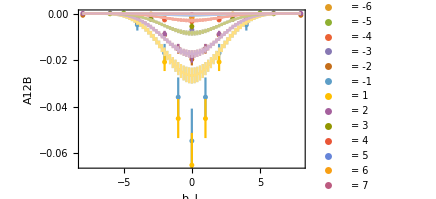

```mathematica
FitAfordiffbLbT[A12B, -1, 8, modelRefit]
```

Re A12B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨-0.069(34)⟩_(2902J), ⟨0.245(79)⟩_(2902J), ⟨0.34(14)⟩_(2902J)}
 chisquareDoF = 2.41171

In (b.P,b^2) spcae:  Re A12B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨-0.069(34)⟩_(2902J),⟨-0.024(17)⟩_(2902J),⟨0.34(14)⟩_(2902J)}

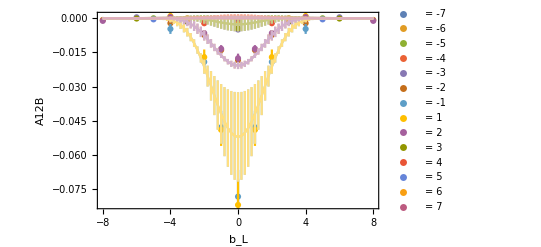

```mathematica
FitAfordiffbLbT[A12B, -2, 8, modelRefit]
```

Re A12B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨-0.058(15)⟩_(2902J), ⟨0.242(62)⟩_(2902J), ⟨0.423(82)⟩_(2902J)}
 chisquareDoF = 0.782222

In (b.P,b^2) spcae:  Re A12B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨-0.058(15)⟩_(2902J),⟨-0.0201(66)⟩_(2902J),⟨0.423(82)⟩_(2902J)}

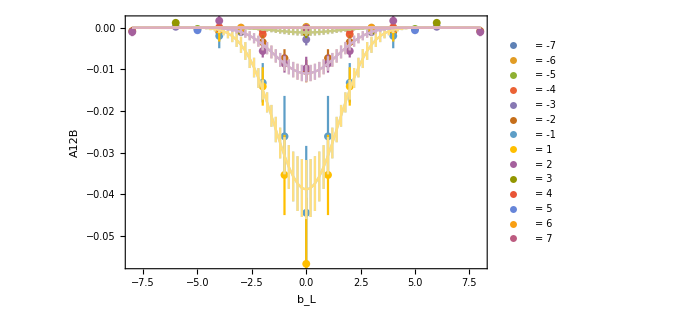

```mathematica
FitAfordiffbLbT[A12B, -3, 8, modelRefit]
```

Re A12B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨-0.031(17)⟩_(2902J), ⟨0.28(22)⟩_(2902J), ⟨0.45(26)⟩_(2902J)}
 chisquareDoF = 0.345898

In (b.P,b^2) spcae:  Re A12B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨-0.031(17)⟩_(2902J),⟨-0.010(17)⟩_(2902J),⟨0.45(26)⟩_(2902J)}

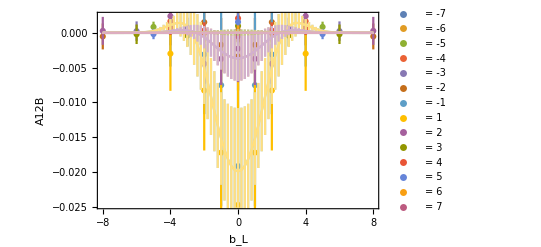

```mathematica
FitAfordiffbLbT[A12B, -4, 8, modelRefit]
```

Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.3724(26)⟩_(2902J), ⟨0.3612(26)⟩_(2902J), ⟨0.4039(29)⟩_(2902J)}
 chisquareDoF = 235.509

In (b.P,b^2) spcae:  Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.3724(26)⟩_(2902J),⟨-0.0427(27)⟩_(2902J),⟨0.4039(29)⟩_(2902J)}

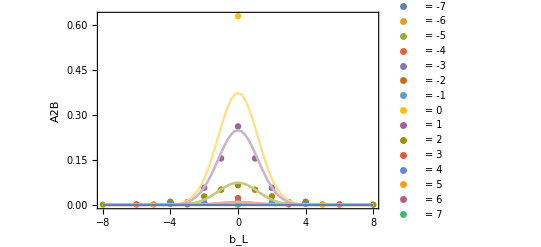

```mathematica
FitAfordiffbLbT[A2B, -1, 8, modelRefit]
```

Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.3693(41)⟩_(2902J), ⟨0.3650(38)⟩_(2902J), ⟨0.4594(54)⟩_(2902J)}
 chisquareDoF = 68.0216

In (b.P,b^2) spcae:  Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.3693(41)⟩_(2902J),⟨-0.0236(12)⟩_(2902J),⟨0.4594(54)⟩_(2902J)}

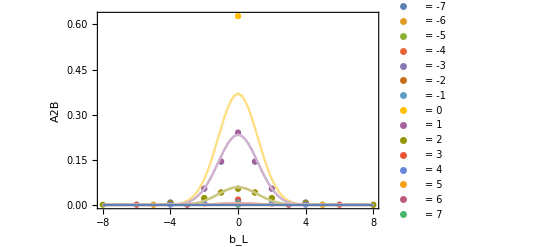

```mathematica
FitAfordiffbLbT[A2B, -2, 8, modelRefit]
```

Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨0.3568(82)⟩_(2902J), ⟨0.3787(72)⟩_(2902J), ⟨0.524(14)⟩_(2902J)}
 chisquareDoF = 14.2587

In (b.P,b^2) spcae:  Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨0.3568(82)⟩_(2902J),⟨-0.0162(13)⟩_(2902J),⟨0.524(14)⟩_(2902J)}

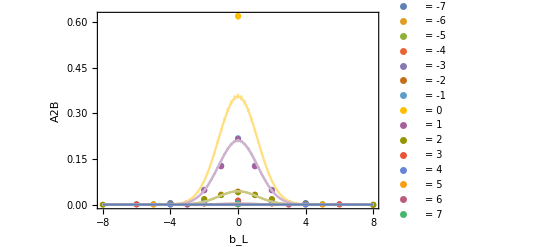

```mathematica
FitAfordiffbLbT[A2B, -3, 8, modelRefit]
```

Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨0.382(19)⟩_(2902J), ⟨0.409(17)⟩_(2902J), ⟨0.580(34)⟩_(2902J)}
 chisquareDoF = 3.22054

In (b.P,b^2) spcae:  Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨0.382(19)⟩_(2902J),⟨-0.0107(19)⟩_(2902J),⟨0.580(34)⟩_(2902J)}

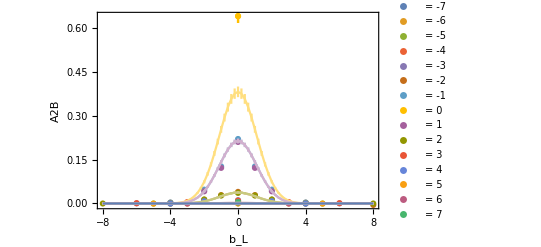

```mathematica
FitAfordiffbLbT[A2B, -4, 8, modelRefit]
```

```mathematica
modelImfit[x1_,x2_,{a_,b_,c_}]:=a*x1*Exp[-b*x1^2]*Exp[-c*x2^2];
FitImAfordiffbLbT[ampname_,P1_, etavalue_, modelfit_]:=(
dataforfit = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
fitJK =JackknifeFit3D[dataforfit,modelfit[bL,bT,{a,b,c}],{a,b, c},{bL,bT}, modelfit];
fitParas=FitParameters/. fitJK;
fitchiDoF=chisquareDoF/. fitJK;
Print["Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",OutputForm[fitParas],"\n chisquareDoF = ", fitchiDoF];
Print["In (b.P,b^2) spcae:  Re ",ampname," =>  = ",P1," ,eta = ", etavalue,"\n Fitting into   -> () = ",{OutputForm[fitParas[[1]]/P1],OutputForm[(fitParas[[2]]-fitParas[[3]])/(P1^2)],OutputForm[fitParas[[3]]] }];
bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->odd}],bL]];
PlotPLforDiffbT={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->odd}],{bL,data}];
AppendTo[PlotPLforDiffbT,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotPLforDiffbT[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{ , ampname}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}]];
fitbandforallbT = {};
Do[
fitbLband = {};
Do[
AppendTo[fitbLband,{bLx, modelfitJackkifband[modelfit, fitParas,bTlist[[bTx]],bLx]}];
,{bLx,Min[bLlist],Max[bLlist],0.2}];
AppendTo[fitbandforallbT,fitbLband];
,{bTx,Length[bTlist]}];
fitPlotbL=Show[PlotbL,Table[ErrorListPlot[MakeErrBars[fitbandforallbT[[bTx]]],PlotStyle->Lighter[ColorData[97,"ColorList"][[Mod[bTx,15]]],0.5],Joined->True, Frame->True],{bTx,Length[bTlist]}]];
(*fitPlotbP=Show[PlotbP,Table[Plot[modelfitJackkife[modelfit, fitParas, Pbx,bsquarelist[[bsqi]]][[1]],{Pbx,Min[Pb32by2Pilist],Max[Pb32by2Pilist]},PlotStyle->ColorData[97,"ColorList"][[Mod[bsqi,15]]]],{bsqi,Length[bsquarelist]}]];*)
Print[fitPlotbL]
)
```

Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨0.00762(80)⟩_(2902J), ⟨0.1305(89)⟩_(2902J), ⟨0.123(19)⟩_(2902J)}
 chisquareDoF = 2.89979

In (b.P,b^2) spcae:  Re A2B =>  = -1 ,eta = 8
 Fitting into   -> () = {⟨-0.00762(80)⟩_(2902J),⟨0.008 ± 0.017⟩_(2902J),⟨0.123(19)⟩_(2902J)}

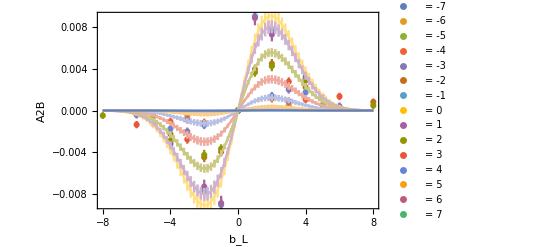

```mathematica
FitImAfordiffbLbT[A2B, -1, 8, modelImfit]
```

Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨0.0154(17)⟩_(2902J), ⟨0.150(11)⟩_(2902J), ⟨0.184(31)⟩_(2902J)}
 chisquareDoF = 2.65799

In (b.P,b^2) spcae:  Re A2B =>  = -2 ,eta = 8
 Fitting into   -> () = {⟨-0.00771(83)⟩_(2902J),⟨-0.0085(65)⟩_(2902J),⟨0.184(31)⟩_(2902J)}

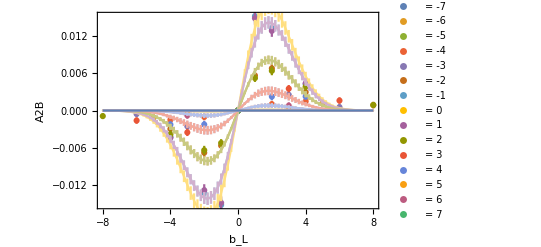

```mathematica
FitImAfordiffbLbT[A2B, -2, 8, modelImfit]
```

Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨0.0241(29)⟩_(2902J), ⟨0.171(19)⟩_(2902J), ⟨0.358(51)⟩_(2902J)}
 chisquareDoF = 0.864426

In (b.P,b^2) spcae:  Re A2B =>  = -3 ,eta = 8
 Fitting into   -> () = {⟨-0.00804(97)⟩_(2902J),⟨-0.0207(52)⟩_(2902J),⟨0.358(51)⟩_(2902J)}

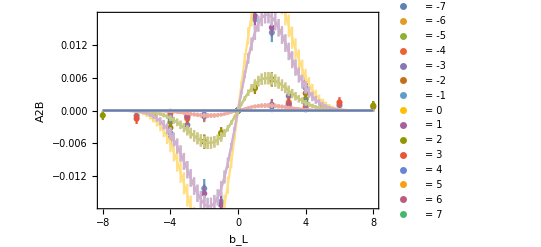

```mathematica
FitImAfordiffbLbT[A2B, -3, 8, modelImfit]
```

Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨0.0262(64)⟩_(2902J), ⟨0.158(32)⟩_(2902J), ⟨0.44(15)⟩_(2902J)}
 chisquareDoF = 0.47948

In (b.P,b^2) spcae:  Re A2B =>  = -4 ,eta = 8
 Fitting into   -> () = {⟨-0.0066(16)⟩_(2902J),⟨-0.0175(84)⟩_(2902J),⟨0.44(15)⟩_(2902J)}

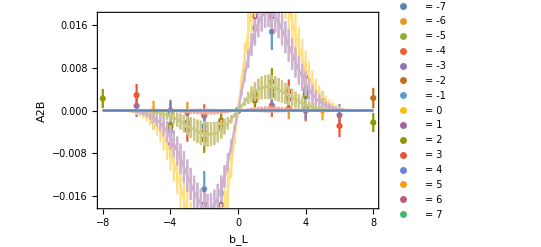

```mathematica
FitImAfordiffbLbT[A2B, -4, 8, modelImfit]
```